```mathematica
(*
Import@"https://raw.githubusercontent.com/jkuczm/MathematicaCellsToTeX/master/NoInstall.m"
PacletInstall@"http://github.com/jkuczm/MathematicaCellsToTeX/releases/download/v0.2.2/CellsToTeX-0.2.2.paclet"
*)
ClearAll["Global`*"];
Needs@"CellsToTeX`";
SetDirectory[NotebookDirectory[]];
Print["Print current directory:"];
Directory[]
(*myPlot=Animate[Plot[Sin[x+a],{x,0,10}],{a,0,5}];
Export["./media/movie0.swf",myPlot];*)
```

Print current directory:

C:\Users\oskat\OneDrive - Instituto Tecnologico y de Estudios Superiores de Monterrey\Documents\MNT_ITESM_courses\1.3.Modelacion_fisica_Matematica\HWork04_Linear_transformations

```mathematica
(*******************************************************************************************************)
```

```mathematica
(*
1.a
T:R^3->R given by T(x,y,z)=1/((x-2)^2+(z-12)^2+(x-2)^2)
Subscript[D, (T)]=R^3
*)
```

Domain:

(x|y|z)∈ℝ&&-4 x+x^2-4 y+y^2-24 z+z^2≠-152

-Graphics3D-

Domain subset Plot:

-Graphics3D-

Range:

Power::infy: Infinite expression 1/0 encountered.

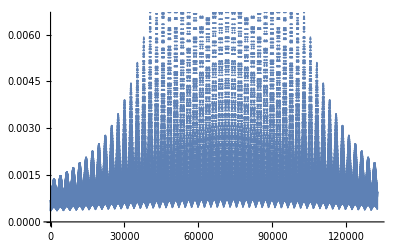

```mathematica
ClearAll["Global`*"];
T=1/((x−2)^2+(z−12)^2+(y−2)^2);

contourLimits=100;
membershipConditions=FunctionDomain[T,{x,y,z}];
domain=ImplicitRegion[membershipConditions,{x,y,z}];

Print["Domain:"];
domainRegion=RegionMember[domain,{x,y,z}]
myPlot=RegionPlot3D[domain,Axes->True]
Export["./media/problem1aDomain.png",myPlot];

Print["Domain subset Plot:"];
(*myPlot=Plot3D[T,{x,y,z}∈domain,Axes->True]
Export["./media/problem1aDomainSubset1.png",myPlot];*)
myPlot=DensityPlot3D[T,{x,y,z}∈domain,Axes->True]
Export["./media/problem1aDomainSubset2.png",myPlot];
(*myPlot=ContourPlot3D[T,{x,y,z}∈domain,Axes->True]
Export["./media/problem1aDomainSubset3.png",myPlot];*)

Print["Range:"];
points=Table[1/((x−2)^2+(z−12)^2+(y−2)^2),{x,-25,25},{y,-25,25},{z,-25,25}];
points=Flatten[points];
ListPlot[points]
(*plots = Table[
Show[Graphics[Point[{n,points[[n]]}]],PlotRange->{{0,500},{0,10}},Axes->Automatic],{n,Length[points]}
];
frames=FoldList[Show,plots];
ListAnimate[frames,AnimationRate->24]

plots = Table[
Plot[{},{x,0,500},PlotRange->{{0,0.001},{0,500}},Epilog->{AbsolutePointSize[3],Point[{n,points[[n]]}]}],{n,Length[points]}
];
frames=FoldList[Show,plots];
ListAnimate[frames,AnimationRate->24]*)
```

```mathematica
(*
1.b
a) Check T preserves sums
let u=(a,b,c), v=(d,e,f) be elements of ℝ^3

T(u+v)=T((a,b,c)+(d,e,f))
=T(a+d,b+e,c+f)
=1/((a+d−2)^2+(c+f−12)^2+(b+e−2)^2)

T(u)+T(v)=T(a,b,c)+T(d,e,f)
=1/((a−2)^2+(c−12)^2+(b−2)^2)+1/((d−2)^2+(f−12)^2+(e−2)^2)

T is NOT a linear transformation since it does not preserve sums.

b) Check T preserves scalars
no need to check ...
*)
```

```mathematica
(*******************************************************************************************************)
```

```mathematica
(*
2.a
T:R^2->R given by W(a,b)=1/(Sin[a/2]+22222/(√(b-1)))
Subscript[D, (T)]=R^2
*)
```

Domain:

(a|b)∈ℝ&&b>1&&22222/(√(-1+b))+Sin[a/2]≠0

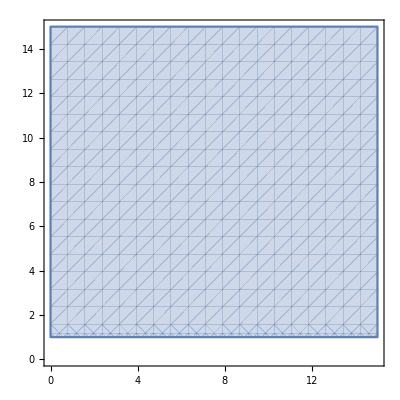

Range:

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

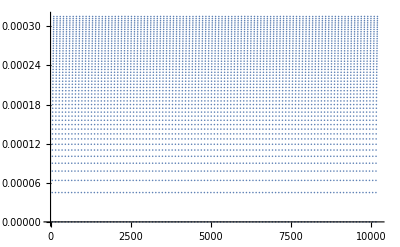

```mathematica
ClearAll["Global`*"];
W=1/(Sin[a/2]+22222/(√(b-1)));

contourLimits=100;
membershipConditions=FunctionDomain[W,{a,b}];
domain=ImplicitRegion[membershipConditions,{a,b}];

Print["Domain:"];
domainRegion=RegionMember[domain,{a,b}]
myPlot=RegionPlot[domainRegion,{a,0,15},{b,0,15},Axes->True]
Export["./media/problem2aDomain.png",myPlot];

(*Print["Domain subset Plot:"];
myPlot=Plot[W,{a,b}∈domain,Axes->True]
Export["./media/problem2aDomainSubset1.png",myPlot];
myPlot=DensityPlot[W,{a,b}∈domain,Axes->True]
Export["./media/problem2aDomainSubset2.png",myPlot];
myPlot=ContourPlot[W,{a,b}∈domain,Axes->True]
Export["./media/problem2aDomainSubset3.png",myPlot];*)

Print["Range:"];
points=Table[1/(Sin[a/2]+22222/(√(b-1))),{a,-50,50},{b,-50,50}];
points=Flatten[points];
ListPlot[points]
(*plots = Table[
Show[Graphics[Point[{n,points[[n]]}]],PlotRange->{{0,500},{0,10}},Axes->Automatic],{n,Length[points]}
];
frames=FoldList[Show,plots];
ListAnimate[frames,AnimationRate->24]

plots = Table[
Plot[{},{x,0,500},PlotRange->{{0,0.001},{0,500}},Epilog->{AbsolutePointSize[3],Point[{n,points[[n]]}]}],{n,Length[points]}
];
frames=FoldList[Show,plots];
ListAnimate[frames,AnimationRate->24]*)
```

```mathematica
]
```

```mathematica
(*
2.b
a) Check T preserves sums
let u=(a,b), v=(d,e) be elements of ℝ^2

T(u+v)=T((a,b)+(d,e))
=T(a+d,b+e)
=1/(Sin[(a+d)/2]+22222/(√(b+e-1)))

T(u)+T(v)=T(a,b)+T(d,e)
=1/(Sin[a/2]+22222/(√(b-1)))+1/(Sin[d/2]+22222/(√(e-1)))

T is NOT a linear transformation since it does not preserve sums.

b) Check T preserves scalars
no need to check ...
*)
```

```mathematica
(*******************************************************************************************************)
```

```mathematica
(*
3.a
A circle can be described as the set of points (x,y) that satisfy x^2+y^2=r^2. Hence, if x=Sin[x]/πⅇ and y=Cos[x]/πⅇ then
x^2+y^2=(Sin[x]/πⅇ)^2+(Cos[x]/πⅇ)^2=r^2 ; where r is the radius.
*)
```

```mathematica
(*3.b*)
ClearAll["Global`*"];
radius=FullSimplify[√((Sin[x]/(π ⅇ))^2+(Cos[x]/(π ⅇ))^2)];
radius
N[%]

(*
The circle equation is in the format (x–h)^2+(y–k)^2=r^2, with the center being at the point (h,k) and the radius being "r". Since h & k are equal to zero, then the center is at the origin.
*)
```

1/(ⅇ π)

0.1171

Range:

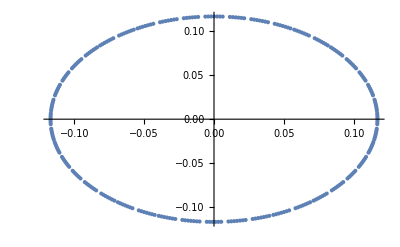

```mathematica
ClearAll["Global`*"];
T={Sin[x]/(π*ⅇ),Cos[x]/(π*ⅇ)};

contourLimits=100;
membershipConditions=FunctionDomain[T,{x}];
domain=ImplicitRegion[membershipConditions,{x}];

(*Print["Domain:"];
domainRegion=RegionMember[domain,{x}]
myPlot=RegionPlot[domainRegion,{x,0,20},{y,0,20},Axes->True]
Export["./media/problem3aDomain.png",myPlot];*)

(*Print["Domain subset Plot:"];
myPlot=Plot[W,{x,y}∈domain,Axes->True]
Export["./media/problem3aDomainSubset1.png",myPlot];
myPlot=DensityPlot[W,{x,y}∈domain,Axes->True]
Export["./media/problem3aDomainSubset2.png",myPlot];
myPlot=ContourPlot[W,{x,y}∈domain,Axes->True]
Export["./media/problem3aDomainSubset3.png",myPlot];*)

Print["Range:"];
points=Table[{Sin[x]/(π*ⅇ),Cos[x]/(π*ⅇ)},{x,-150,150}];
(*points=Flatten[points];*)
ListPlot[points]
plots = Table[
Show[Graphics[Point[points[[n]]]],PlotRange->{{-0.12,0.12},{-0.12,0.12}},Axes->Automatic],{n,Length[points]}
];
frames=FoldList[Show,plots];
myPlot=ListAnimate[frames,AnimationRate->60]
Export["./media/problem3aRange.swf",myPlot];
```

```mathematica
(*******************************************************************************************************)
```

Domain:

(a|b)∈ℝ

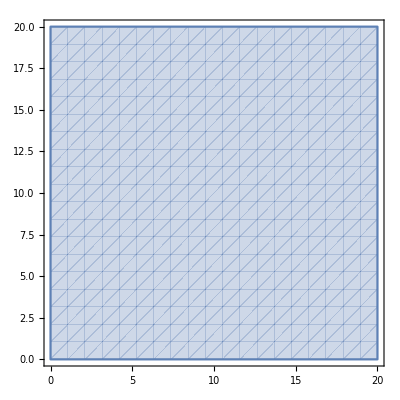

Range:

{2601,2}

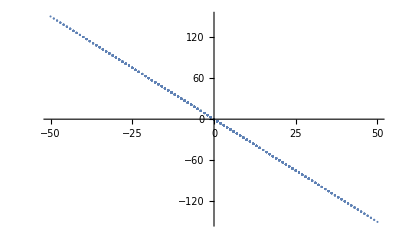

```mathematica
(*4*)
ClearAll["Global`*"];
Ntrans={a-b,3b-3a};

contourLimits=100;
membershipConditions=FunctionDomain[Ntrans,{a,b}];
domain=ImplicitRegion[membershipConditions,{a,b}];

Print["Domain:"];
domainRegion=RegionMember[domain,{a,b}]
myPlot=RegionPlot[domainRegion,{a,0,20},{b,0,20},Axes->True]
Export["./media/problem4aDomain.png",myPlot];

(*Print["Domain subset Plot:"];
myPlot=Plot[W,{x,y}∈domain,Axes->True]
Export["./media/problem3aDomainSubset1.png",myPlot];
myPlot=DensityPlot[W,{x,y}∈domain,Axes->True]
Export["./media/problem3aDomainSubset2.png",myPlot];
myPlot=ContourPlot[W,{x,y}∈domain,Axes->True]
Export["./media/problem3aDomainSubset3.png",myPlot];*)

Print["Range:"];
points=Table[{a-b,3b-3a},{a,-50,50},{b,-50,50}];
points=Flatten[points,1];
Dimensions[points]
ListPlot[points]
plots = Table[
Show[Graphics[Point[points[[n]]]],PlotRange->{{-100,100},{-100,100}},Axes->Automatic],{n,Length[points]}
];
frames=FoldList[Show,plots];
myPlot=ListAnimate[frames,AnimationRate->60]
Export["./media/problem4aRange.swf",myPlot];
```

```mathematica
(*******************************************************************************************************)
```

```mathematica
(* 7
M:R^2->R given by M(x,y)=x+y+2
a) Check M preserves sums
let u=(a,b), v=(d,e) be elements of ℝ^2

M(u+v)=M((a,b)+(d,e))
=M(a+d,b+e)
=a+d+b+e+2

M(u)+M(v)=M(a,b)+M(d,e)
=a+b+2+d+e+2
=a+b+d+e+4

M is NOT a linear transformation since it does not preserve sums.

b) Check M preserves scalars
no need to check ...
*)
```

```mathematica
(*******************************************************************************************************)
```

```mathematica
(* 8
Q:R^2->R^3 given by Q(x,y)=(x,y,√2+√31)
a) Check Q preserves sums
let u=(a,b), v=(d,e) be elements of ℝ^2

Q(u+v)=Q((a,b)+(d,e))
=Q(a+d,b+e)
=(a+d,b+e,√2+√31)

Q(u)+Q(v)=Q(a,b)+Q(d,e)
=(a,b,√2+√31)+(d,e,√2+√31)
=(a+d,b+e,2 √2+2 √31)

Q is NOT a linear transformation since it does not preserve sums.

b) Check Q preserves scalars
no need to check ...
*)
```

```mathematica
(*******************************************************************************************************)
```

```mathematica
(*
GET LaTeX CODE
*)
Notebooks[]
nbObj=Notebooks[][[2]]
(*Swich off auto deleting of labels, so that we can extract some data from them.*)CurrentValue[nbObj,CellLabelAutoDelete]=False;
SelectionMove[nbObj,All,Notebook];
(*SelectionEvaluate[nbObj,Before];*)
SetOptions[CellToTeX,"CurrentCellIndex"->Automatic];
ExportString[NotebookGet[nbObj]/.cell:Cell[_,__]:>Cell[CellToTeX[cell],"Final"],"TeX","FullDocument"->False,"ConversionRules"->{"Final"->Identity}]
```

{3fi8m_shm15FrontEndObject[LinkObject["3fi8m_shm", 3, 1]]15Basic Math AssistantC:\Program Files\Wolfram Research\Mathematica\11.3\SystemFiles\FrontEnd\Palettes\BasicMathAssistant.nb,3fi8m_shm20FrontEndObject[LinkObject["3fi8m_shm", 3, 1]]20HWork04_Linear_transformations.nbC:\Users\oskat\OneDrive - Instituto Tecnologico y de Estudios Superiores de Monterrey\Documents\MNT_ITESM_courses\1.3.Modelacion_fisica_Matematica\HWork04_Linear_transformations\HWork04_Linear_transformations.nb,3fi8m_shm1FrontEndObject[LinkObject["3fi8m_shm", 3, 1]]1Messages}

3fi8m_shm20FrontEndObject[LinkObject["3fi8m_shm", 3, 1]]20HWork04_Linear_transformations.nbC:\Users\oskat\OneDrive - Instituto Tecnologico y de Estudios Superiores de Monterrey\Documents\MNT_ITESM_courses\1.3.Modelacion_fisica_Matematica\HWork04_Linear_transformations\HWork04_Linear_transformations.nb

CellsToTeXException::unsupported: Box: Graphics3DBox[GraphicsComplex3DBox[{{-15.,-12.7143,-7.71429},{-15.,-12.7143,-10.},{-12.7143,-15.,-7.71429},{-12.7143,-12.7143,-10.},{-15.,-15.,-5.42857},«42»,{-15.,-10.4286,-5.42857},{-15.,-10.4286,-3.14286},{-15.,-10.4286,-0.857143},«422»},{{RGBColor[0.880722, 0.611041, 0.142051],«3»},{},{},{},{}}],«7»] is not one of supported: {RowBox[_List],(StyleBox|ButtonBox|InterpretationBox|FormBox|TagBox|TooltipBox)[_,___],TemplateBox[_,_,___],GridBox[{___List},___],«10»,HoldPattern[FractionBox[Repeated[_,{2}],OptionsPattern[]]],HoldPattern[SqrtBox[Repeated[_,{1}],OptionsPattern[]]],HoldPattern[RadicalBox[Repeated[_,{2}],OptionsPattern[]]],_String}. Exception occurred in CellsToTeX`Configuration`boxesToTeXProcessor[{BoxRules→{RowBox[CellsToTeX`Private`l:Blank[«1»]]:>CellsToTeX`Configuration`makeString[CellsToTeX`Private`l],«16»,CellsToTeX`Private`str$_String:>StringReplace[CellsToTeX`Configuration`makeStringDefault[CellsToTeX`Private`str$],{Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],RuleDelayed[«2»]}]},…→«1»,{TeXOptions→{},«3»,{{«1»},{CellChangeTimes→{«1»},CellLabel→Out[1426]=}}}}].

CellsToTeXException::unsupported: Box: Graphics3DBox[Raster3DBox[«1»],Axes→True,AxesLabel→{None,None,None},BoxRatios→{1,1,1},FaceGridsStyle→Automatic,PlotRange→{{-15.,17.},{-15.,17.},{-10.,22.}},Ticks→{Automatic,Automatic,Automatic}] is not one of supported: {RowBox[_List],(StyleBox|ButtonBox|InterpretationBox|FormBox|TagBox|TooltipBox)[_,___],TemplateBox[_,_,___],GridBox[{___List},___],«10»,HoldPattern[FractionBox[Repeated[_,{2}],OptionsPattern[]]],HoldPattern[SqrtBox[Repeated[_,{1}],OptionsPattern[]]],HoldPattern[RadicalBox[Repeated[_,{2}],OptionsPattern[]]],_String}. Exception occurred in CellsToTeX`Configuration`boxesToTeXProcessor[{BoxRules→{RowBox[CellsToTeX`Private`l:Blank[«1»]]:>CellsToTeX`Configuration`makeString[CellsToTeX`Private`l],«16»,CellsToTeX`Private`str$_String:>StringReplace[CellsToTeX`Configuration`makeStringDefault[CellsToTeX`Private`str$],{Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],RuleDelayed[«2»]}]},…s→«1»,{TeXOptions→{addtoindex→3},«3»,{{«1»},{CellChangeTimes→{«1»},«9»→…=}}}}].

CellsToTeXException::unsupported: Box: DynamicBox[ToBoxes[Refresh[Internal`MessageMenu[Power,infy,2,1432,780,22354720829223618230,Local],None],StandardForm],Evaluator→FEPrivate`If[FEPrivate`EvaluatorStatus[Local]===Running,Local,FrontEnd`CurrentValue[FrontEnd`$FrontEnd,Evaluator]],ImageSizeCache→{20.,{3.,11.}},SingleEvaluation→True] is not one of supported: {RowBox[_List],(StyleBox|ButtonBox|InterpretationBox|FormBox|TagBox|TooltipBox)[_,___],TemplateBox[_,_,___],GridBox[{___List},___],«10»,HoldPattern[FractionBox[Repeated[_,{2}],OptionsPattern[]]],HoldPattern[SqrtBox[Repeated[_,{1}],OptionsPattern[]]],HoldPattern[RadicalBox[Repeated[_,{2}],OptionsPattern[]]],_String}. Exception occurred in CellsToTeX`Configuration`boxesToTeXProcessor[«1»].

General::stop: Further output of CellsToTeXException::unsupported will be suppressed during this calculation.

\begin{mmaCell}{Input}\r
  \r
  (*\r
  Import@"https://raw.githubusercontent.com/jkuczm/MathematicaCellsToTeX/master/NoInstall.m"\r
  PacletInstall@"http://github.com/jkuczm/MathematicaCellsToTeX/releases/download/v0.2.2/CellsToTeX-0.2.2.paclet"\r
  *)\r
  ClearAll["Global`*"];\r
  Needs@"CellsToTeX`";\r
  SetDirectory[NotebookDirectory[]];\r
  Print["Print current directory:"];\r
  Directory[]\r
  (*myPlot=Animate[Plot[Sin[x+a],\{x,0,10\}],\{a,0,5\}];\r
  Export["./media/movie0.swf",myPlot];*)\r
\end{mmaCell}\r
\r
\begin{mmaCell}{Print}\r
  Print current directory:\r
\end{mmaCell}\r
\r
\begin{mmaCell}[addtoindex=4]{Output}\r
  C:\textbackslash{}Users\textbackslash{}oskat\textbackslash{}OneDrive - Instituto Tecnologico y de Estudios Superiores de Monterrey\textbackslash{}Documents\textbackslash{}MNT_ITESM_courses\textbackslash{}1.3.Modelacion_fisica_Matematica\textbackslash{}HWork04_Linear_transformations\r
\end{mmaCell}\r
\r
\begin{mmaCell}{Input}\r
  (*******************************************************************************************************)\r
\end{mmaCell}\r
\r
\begin{mmaCell}{Input}\r
  (*\r
  1.a\r
  T:\mmaSup{R}{3}\(\pmb{\rightarrow}\)R given by T(x,y,z)=\mmaFrac{1}{\mmaSup{(x-2)}{2}+\mmaSup{(z-12)}{2}+\mmaSup{(x-2)}{2}}\r
  \mmaSub{D}{(T)}=\mmaSup{R}{3}\r
  *)\r
\end{mmaCell}\r
\r
\begin{mmaCell}[addtoindex=1406]{Input}\r
  ClearAll["Global`*"];\r
  T=\mmaFrac{1}{(x-2)^2+(z-12)^2+(y-2)^2};\r
  \r
  contourLimits=100;\r
  membershipConditions=FunctionDomain[T,\{x,y,z\}];\r
  domain=ImplicitRegion[membershipConditions,\{x,y,z\}];\r
  \r
  Print["Domain:"];\r
  domainRegion=RegionMember[domain,\{x,y,z\}]\r
  myPlot=RegionPlot3D[domain,Axes\(\pmb{\to}\)True]\r
  Export["./media/problem1aDomain.png",myPlot];\r
  \r
  Print["Domain subset Plot:"];\r
  (*myPlot=Plot3D[T,\{x,y,z\}\(\pmb{\in}\)domain,Axes\(\pmb{\to}\)True]\r
  Export["./media/problem1aDomainSubset1.png",myPlot];*)\r
  myPlot=DensityPlot3D[T,\{x,y,z\}\(\pmb{\in}\)domain,Axes\(\pmb{\to}\)True]\r
  Export["./media/problem1aDomainSubset2.png",myPlot];\r
  (*myPlot=ContourPlot3D[T,\{x,y,z\}\(\pmb{\in}\)domain,Axes\(\pmb{\to}\)True]\r
  Export["./media/problem1aDomainSubset3.png",myPlot];*)\r
  \r
  Print["Range:"];\r
  points=Table[\mmaFrac{1}{(\mmaFnc{x}-2)^2+(\mmaFnc{z}-12)^2+(\mmaFnc{y}-2)^2},\{\mmaFnc{x},-25,25\},\{\mmaFnc{y},-25,25\},\{\mmaFnc{z},-25,25\}];\r
  points=Flatten[points];\r
  ListPlot[points]\r
  (*plots = Table[\r
  Show[Graphics[Point[\{n,points[[n]]\}]],PlotRange\(\pmb{\to}\)\{\{0,500\},\{0,10\}\},Axes\(\pmb{\to}\)Automatic],\{n,Length[points]\}\r
  ];\r
  frames=FoldList[Show,plots];\r
  ListAnimate[frames,AnimationRate\(\pmb{\to}\)24]\r
  \r
  plots = Table[\r
  Plot[\{\},\{x,0,500\},PlotRange\(\pmb{\to}\)\{\{0,0.001\},\{0,500\}\},Epilog\(\pmb{\to}\)\{AbsolutePointSize[3],Point[\{n,points[[n]]\}]\}],\{n,Length[points]\}\r
  ];\r
  frames=FoldList[Show,plots];\r
  ListAnimate[frames,AnimationRate\(\pmb{\to}\)24]*)\r
\end{mmaCell}\r
\r
\begin{mmaCell}{Print}\r
  Domain:\r
\end{mmaCell}\r
\r
\begin{mmaCell}[addtoindex=6]{Output}\r
  (x|y|z)\(\in\mathbb{R}\)&&-4 x+\mmaSup{x}{2}-4 y+\mmaSup{y}{2}-24 z+\mmaSup{z}{2}\(\neq\)-152\r
\end{mmaCell}\r
\r
\begin{mmaCell}{Print}\r
  Domain subset Plot:\r
\end{mmaCell}\r
\r
\begin{mmaCell}{Print}\r
  Range:\r
\end{mmaCell}\r
\r
\begin{mmaCell}{Input}\r
  (*\r
  1.b\r
  a) Check T preserves sums\r
  let u=(a,b,c), v=(d,e,f) be elements of \mmaSup{\mmaUnd{\(\pmb{\mathbb{R}}\)}}{3}\r
  \r
  T(u+v)=T((a,b,c)+(d,e,f))\r
  =T(a+d,b+e,c+f)\r
  =\mmaFrac{1}{\mmaSup{(a+d-2)}{2}+\mmaSup{(c+f-12)}{2}+\mmaSup{(b+e-2)}{2}}\r
  \r
  T(u)+T(v)=T(a,b,c)+T(d,e,f)\r
  =\mmaFrac{1}{\mmaSup{(a-2)}{2}+\mmaSup{(c-12)}{2}+\mmaSup{(b-2)}{2}}+\mmaFrac{1}{\mmaSup{(d-2)}{2}+\mmaSup{(f-12)}{2}+\mmaSup{(e-2)}{2}}\r
  \r
  T is NOT a linear transformation since it does not preserve sums.\r
  \r
  b) Check T preserves scalars\r
  no need to check ...\r
  *)\r
\end{mmaCell}\r
\r
\begin{mmaCell}{Input}\r
  (*******************************************************************************************************)\r
\end{mmaCell}\r
\r
\begin{mmaCell}{Input}\r
  (*\r
  2.a\r
  T:\mmaSup{R}{2}\(\pmb{\rightarrow}\)R given by W(a,b)=\mmaFrac{1}{Sin[\mmaFrac{a}{2}]+\mmaFrac{22222}{\mmaSqrt{b-1}}}\r
  \mmaSub{D}{(T)}=\mmaSup{R}{2}\r
  *)\r
\end{mmaCell}\r
\r
\begin{mmaCell}[addtoindex=171]{Input}\r
  ClearAll["Global`*"];\r
  W=\mmaFrac{1}{Sin[\mmaFrac{a}{2}]+\mmaFrac{22222}{\mmaSqrt{b-1}}};\r
  \r
  contourLimits=100;\r
  membershipConditions=FunctionDomain[W,\{a,b\}];\r
  domain=ImplicitRegion[membershipConditions,\{a,b\}];\r
  \r
  Print["Domain:"];\r
  domainRegion=RegionMember[domain,\{a,b\}]\r
  myPlot=RegionPlot[domainRegion,\{\mmaFnc{a},0,15\},\{\mmaFnc{b},0,15\},Axes\(\pmb{\to}\)True]\r
  Export["./media/problem2aDomain.png",myPlot];\r
  \r
  (*Print["Domain subset Plot:"];\r
  myPlot=Plot[W,\{a,b\}\(\pmb{\in}\)domain,Axes\(\pmb{\to}\)True]\r
  Export["./media/problem2aDomainSubset1.png",myPlot];\r
  myPlot=DensityPlot[W,\{a,b\}\(\pmb{\in}\)domain,Axes\(\pmb{\to}\)True]\r
  Export["./media/problem2aDomainSubset2.png",myPlot];\r
  myPlot=ContourPlot[W,\{a,b\}\(\pmb{\in}\)domain,Axes\(\pmb{\to}\)True]\r
  Export["./media/problem2aDomainSubset3.png",myPlot];*)\r
  \r
  Print["Range:"];\r
  points=Table[\mmaFrac{1}{Sin[\mmaFrac{\mmaFnc{a}}{2}]+\mmaFrac{22222}{\mmaSqrt{\mmaFnc{b}-1}}},\{\mmaFnc{a},-50,50\},\{\mmaFnc{b},-50,50\}];\r
  points=Flatten[points];\r
  ListPlot[points]\r
  (*plots = Table[\r
  Show[Graphics[Point[\{n,points[[n]]\}]],PlotRange\(\pmb{\to}\)\{\{0,500\},\{0,10\}\},Axes\(\pmb{\to}\)Automatic],\{n,Length[points]\}\r
  ];\r
  frames=FoldList[Show,plots];\r
  ListAnimate[frames,AnimationRate\(\pmb{\to}\)24]\r
  \r
  plots = Table[\r
  Plot[\{\},\{x,0,500\},PlotRange\(\pmb{\to}\)\{\{0,0.001\},\{0,500\}\},Epilog\(\pmb{\to}\)\{AbsolutePointSize[3],Point[\{n,points[[n]]\}]\}],\{n,Length[points]\}\r
  ];\r
  frames=FoldList[Show,plots];\r
  ListAnimate[frames,AnimationRate\(\pmb{\to}\)24]*)\r
\end{mmaCell}\r
\r
\begin{mmaCell}{Print}\r
  Domain:\r
\end{mmaCell}\r
\r
\begin{mmaCell}[addtoindex=6]{Output}\r
  (a|b)\(\in\mathbb{R}\)&&b>1&&\mmaFrac{22222}{\mmaSqrt{-1+b}}+Sin[\mmaFrac{a}{2}]\(\neq\)0\r
\end{mmaCell}\r
\r
\begin{mmaCell}{Print}\r
  Range:\r
\end{mmaCell}\r
\r
\begin{mmaCell}{Input}\r
  ]\r
\end{mmaCell}\r
\r
\begin{mmaCell}{Input}\r
  (*\r
  2.b\r
  a) Check T preserves sums\r
  let u=(a,b), v=(d,e) be elements of \mmaSup{\mmaUnd{\(\pmb{\mathbb{R}}\)}}{2}\r
  \r
  T(u+v)=T((a,b)+(d,e))\r
  =T(a+d,b+e)\r
  =\mmaFrac{1}{Sin[\mmaFrac{a+d}{2}]+\mmaFrac{22222}{\mmaSqrt{b+e-1}}}\r
  \r
  T(u)+T(v)=T(a,b)+T(d,e)\r
  =\mmaFrac{1}{Sin[\mmaFrac{a}{2}]+\mmaFrac{22222}{\mmaSqrt{b-1}}}+\mmaFrac{1}{Sin[\mmaFrac{d}{2}]+\mmaFrac{22222}{\mmaSqrt{e-1}}}\r
  \r
  T is NOT a linear transformation since it does not preserve sums.\r
  \r
  b) Check T preserves scalars\r
  no need to check ...\r
  *)\r
\end{mmaCell}\r
\r
\begin{mmaCell}{Input}\r
  (*******************************************************************************************************)\r
\end{mmaCell}\r
\r
\begin{mmaCell}{Input}\r
  (*\r
  3.a\r
  A circle can be described as the set of points (x,y) that satisfy \mmaSup{x}{2}+\mmaSup{y}{2}=\mmaSup{r}{2}. Hence, if x=\mmaFrac{Sin[x]}{\(\pmb{\pi}\)e}\r
and y=\mmaFrac{Cos[x]}{\(\pmb{\pi}\)e} then\r
  \mmaSup{x}{2}+\mmaSup{y}{2}=\mmaSup{(\mmaFrac{Sin[x]}{\(\pmb{\pi}\)e})}{2}+\mmaSup{(\mmaFrac{Cos[x]}{\(\pmb{\pi}\)e})}{2}=\mmaSup{r}{2} ; where\r
r is the radius.\r
  *)\r
\end{mmaCell}\r
\r
\begin{mmaCell}[addtoindex=-33]{Input}\r
  (*3.b*)\r
  ClearAll["Global`*"];\r
  radius=FullSimplify[\mmaSqrt{\mmaSup{(\mmaFrac{Sin[x]}{\mmaDef{\(\pmb{\pi}\)} \mmaDef{e}})}{2}+\mmaSup{(\mmaFrac{Cos[x]}{\mmaDef{\(\pmb{\pi}\)}\r
\mmaDef{e}})}{2}}];\r
  radius\r
  N[%]\r
  \r
  (*\r
  The circle equation is in the format \mmaSup{(x--h)}{2}+\mmaSup{(y--k)}{2}=\mmaSup{r}{2}, with the center being at the point (h,k) and the radius\r
being "r". Since h & k are equal to zero, then the center is at the origin.\r
  *)\r
\end{mmaCell}\r
\r
\begin{mmaCell}[addtoindex=2]{Output}\r
  \mmaFrac{1}{e \(\pi\)}\r
\end{mmaCell}\r
\r
\begin{mmaCell}{Output}\r
  0.11709966304863834`\r
\end{mmaCell}\r
\r
\begin{mmaCell}[morefunctionlocal={n}]{Input}\r
  ClearAll["Global`*"];\r
  T=\{\mmaFrac{Sin[x]}{\mmaDef{\(\pmb{\pi}\)}*\mmaDef{e}},\mmaFrac{Cos[x]}{\mmaDef{\(\pmb{\pi}\)}*\mmaDef{e}}\};\r
  \r
  contourLimits=100;\r
  membershipConditions=FunctionDomain[T,\{x\}];\r
  domain=ImplicitRegion[membershipConditions,\{x\}];\r
  \r
  (*Print["Domain:"];\r
  domainRegion=RegionMember[domain,\{x\}]\r
  myPlot=RegionPlot[domainRegion,\{x,0,20\},\{y,0,20\},Axes\(\pmb{\to}\)True]\r
  Export["./media/problem3aDomain.png",myPlot];*)\r
  \r
  (*Print["Domain subset Plot:"];\r
  myPlot=Plot[W,\{x,y\}\(\pmb{\in}\)domain,Axes\(\pmb{\to}\)True]\r
  Export["./media/problem3aDomainSubset1.png",myPlot];\r
  myPlot=DensityPlot[W,\{x,y\}\(\pmb{\in}\)domain,Axes\(\pmb{\to}\)True]\r
  Export["./media/problem3aDomainSubset2.png",myPlot];\r
  myPlot=ContourPlot[W,\{x,y\}\(\pmb{\in}\)domain,Axes\(\pmb{\to}\)True]\r
  Export["./media/problem3aDomainSubset3.png",myPlot];*)\r
  \r
  Print["Range:"];\r
  points=Table[\{\mmaFrac{Sin[\mmaFnc{x}]}{\mmaDef{\(\pmb{\pi}\)}*\mmaDef{e}},\mmaFrac{Cos[\mmaFnc{x}]}{\mmaDef{\(\pmb{\pi}\)}*\mmaDef{e}}\},\{\mmaFnc{x},-150,150\}];\r
  (*points=Flatten[points];*)\r
  ListPlot[points]\r
  plots = Table[\r
  Show[Graphics[Point[points[[n]]]],PlotRange\(\pmb{\to}\)\{\{-0.12,0.12\},\{-0.12,0.12\}\},Axes\(\pmb{\to}\)Automatic],\{n,Length[points]\}\r
  ];\r
  frames=FoldList[Show,plots];\r
  myPlot=ListAnimate[frames,AnimationRate\(\pmb{\to}\)60]\r
  Export["./media/problem3aRange.swf",myPlot];\r
\end{mmaCell}\r
\r
\begin{mmaCell}{Print}\r
  Range:\r
\end{mmaCell}\r
\r
\begin{mmaCell}{Input}\r
  (*******************************************************************************************************)\r
\end{mmaCell}\r
\r
\begin{mmaCell}{Input}\r
  (* 7\r
  M:\mmaSup{R}{2}\(\pmb{\rightarrow}\)R given by M(x,y)=x+y+2\r
  a) Check M preserves sums\r
  let u=(a,b), v=(d,e) be elements of \mmaSup{\(\pmb{\mathbb{R}}\)}{2}\r
  \r
  M(u+v)=M((a,b)+(d,e))\r
  =M(a+d,b+e)\r
  =a+d+b+e+2\r
  \r
  M(u)+M(v)=M(a,b)+M(d,e)\r
  =a+b+2+d+e+2\r
  =a+b+d+e+4\r
  \r
  M is NOT a linear transformation since it does not preserve sums.\r
  \r
  b) Check M preserves scalars\r
  no need to check ...\r
  *)\r
\end{mmaCell}\r
\r
\begin{mmaCell}{Input}\r
  (*******************************************************************************************************)\r
\end{mmaCell}\r
\r
\begin{mmaCell}{Input}\r
  (* 8\r
  Q:\mmaSup{R}{2}\(\pmb{\rightarrow}\)\mmaSup{R}{3} given by Q(x,y)=(x,y,\mmaSqrt{2}+\mmaSqrt{31})\r
  a) Check Q preserves sums\r
  let u=(a,b), v=(d,e) be elements of \mmaSup{\(\pmb{\mathbb{R}}\)}{2}\r
  \r
  Q(u+v)=Q((a,b)+(d,e))\r
  =Q(a+d,b+e)\r
  =(a+d,b+e,\mmaSqrt{2}+\mmaSqrt{31})\r
  \r
  T(u)+T(v)=T(a,b)+T(d,e)\r
  =(a,b,\mmaSqrt{2}+\mmaSqrt{31})+(d,e,\mmaSqrt{2}+\mmaSqrt{31})\r
  =(a+d,b+e,2 \mmaSqrt{2}+2 \mmaSqrt{31})\r
  \r
  T is NOT a linear transformation since it does not preserve sums.\r
  \r
  b) Check T preserves scalars\r
  no need to check ...\r
  *)\r
\end{mmaCell}\r
\r
\begin{mmaCell}{Input}\r
  (*******************************************************************************************************)\r
\end{mmaCell}\r
\r
\begin{mmaCell}[addtoindex=-1577,moredefined={nbObj, CellToTeX},morepattern={cell}]{Input}\r
  (*\r
  GET LaTeX CODE\r
  *)\r
  Notebooks[]\r
  nbObj=Notebooks[][[2]]\r
  (*Swich off auto deleting of labels, so that we can extract some data from them.*)CurrentValue[nbObj,CellLabelAutoDelete]=False;\r
  SelectionMove[nbObj,All,Notebook];\r
  (*SelectionEvaluate[nbObj,Before];*)\r
  SetOptions[CellToTeX,"CurrentCellIndex"\(\pmb{\to}\)Automatic];\r
  ExportString[NotebookGet[nbObj]/.cell:Cell[_,__]\(\pmb{:\to}\)Cell[CellToTeX[cell],"Final"],"TeX","FullDocument"\(\pmb{\to}\)False,"ConversionRules"\(\pmb{\to}\)\{"Final"\(\pmb{\to}\)Identity\}]\r
\end{mmaCell}\r
\r